### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[]
```

We can pull out the ruleset itself:

```mathematica
rs[["RuleSet"]]
```

We generate the sessie and its causal network, again giving it a convenient name:

```mathematica
sss=SSS[rs[["RuleSet"]], "A",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,25]
```

```mathematica
nds[[1;;349]]
```

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;349]]]
```

The most compressed part is

```mathematica
{ExpandAll[%]}
```

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

===
Experimenting with Sessies
6308190100: {“AB” -> “BA”, “AA” -> “B”, “B” -> “AAA”}
6355450520: {“ABB” -> “AAA”, “A” -> “B”, “B” -> “AA”}
642296934875: {“A” -> “BC”, “CB” -> “A”, “B” -> “AAAA”}
702927424475: {“AA” -> “”, “AB” -> “BA”, “A” -> “BB”, “B” -> “AAA”}

```mathematica
rs01 = FromReducedRankIndex[6308190100]
rs02 = FromReducedRankIndex[6355450520]
rs03 = FromReducedRankIndex[642296934875]
rs04 = FromReducedRankIndex[702927424475]
```

<|Index→6308190100,QCode→34243232424233,RuleSet→{AB→BA,AA→B,B→AAA}|>

<|Index→6355450520,QCode→34342332242423,RuleSet→{ABB→AAA,A→B,B→AA}|>

<|Index→642296934875,QCode→24344244342242333,RuleSet→{A→BC,CB→A,B→AAAA}|>

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>




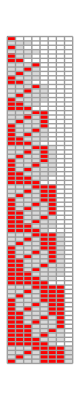
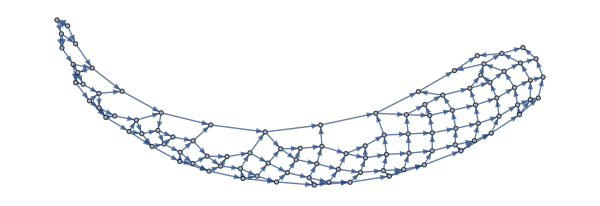
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs01[["RuleSet"]], "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,500.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
rs01[["RuleSet"]]
SSSInitialState[rs01[["RuleSet"]]]
```

{AB→BA,AA→B,B→AAA}

AABAB

```mathematica
netds = ToNetDifferenceSets[sss[["Net"]]];
reduced = ReduceSetList[netds]
```

{{1,1,4},{1},{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^5[€^2[{1,3}],{3,28}],€^3[€^2[{1,3}],{3}],€_(n$1⊨1)^2[{1,4-2 (-1+n$1)}],{1},€^2[{}],{1,2,3},€^3[€^2[{1,3}],{3}],€^2[{1,3}],{},{1}}